```mathematica
MyMax=7
```

7

```mathematica
Edges[sets_]:=Select[sets,Length[#]==Length[Flatten[#]]-1&]
```

```mathematica
GraphFromEdges2[edges_]:=Block[{h,g,size,current,comp},
Graph[Range[MyMax],edges, VertexLabels->"Name"]
]
```

```mathematica
FactorInteger[2097152]
```

{{2,21}}

```mathematica
2^TriangleNumber[7]
```

2^TriangleNumber[7]

```mathematica
all2=Monitor[Table[GraphFromEdges2[Map[#[[1]]<->#[[2]]&,set]],{set,Subsets[Subsets[Range[MyMax],{2}]]}],set];
```

```mathematica
Length[all2]
```

2097152

```mathematica
all1=Tally[all2,IsomorphicGraphQ];Length[all1]
```

1044

```mathematica
.
```

```mathematica
all=Map[First,all1];Length[all]
```

1044

```mathematica
ChromaticNumber[g_]:=Max[Select[Map[Last,With[{r=Roots[ChromaticPolynomial[g,x]==0,x]},Table[r[[k]],{k,1,Length[r]}]]],Element[#,Integers]&]]+1
```

```mathematica
CliqueNumber[g_]:=Length[First[FindClique[g]]]
```

```mathematica
Map[{CliqueNumber[#], ChromaticNumber[#]}&,all]//Tally//Sort
```

{{{1,1},1},{{2,2},87},{{2,3},19},{{3,3},560},{{3,4},18},{{4,4},300},{{4,5},1},{{5,5},51},{{6,6},6},{{7,7},1}}

```mathematica
CliqueNumber[CompleteGraph[5]]
```

5

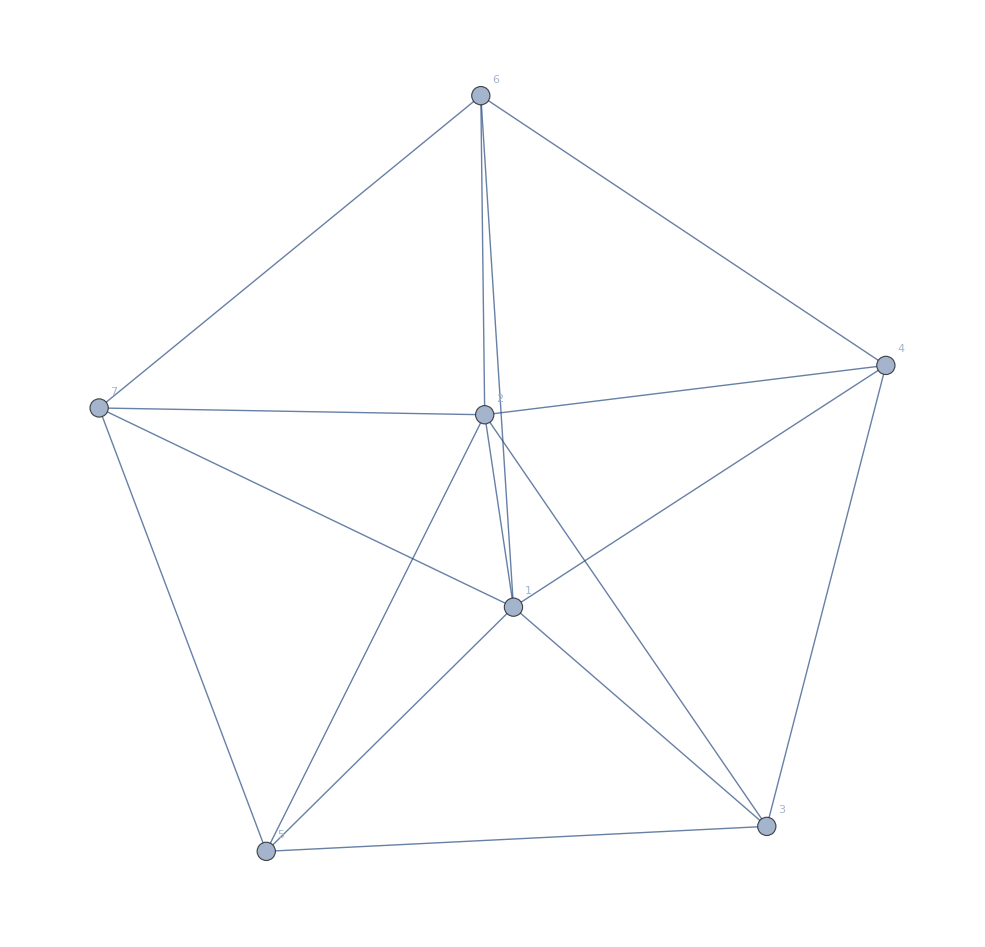

```mathematica
Select[all,CliqueNumber[#]==4&&ChromaticNumber[#]==5&]
```

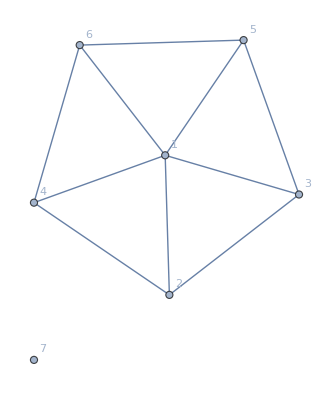
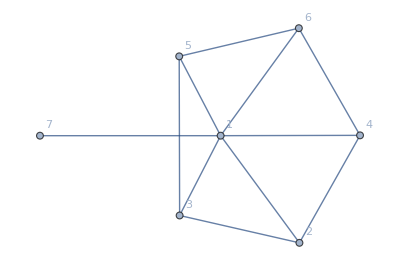
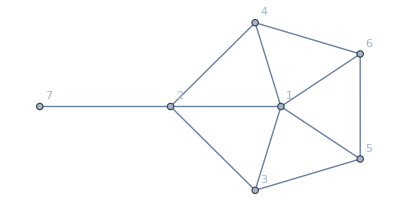
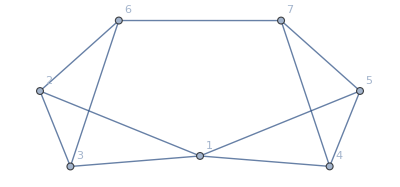
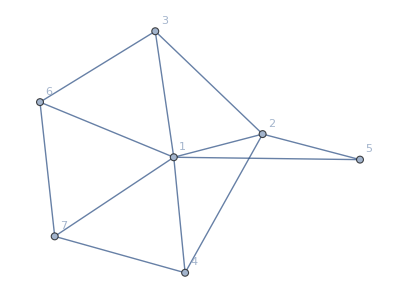
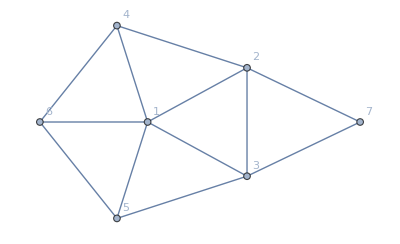
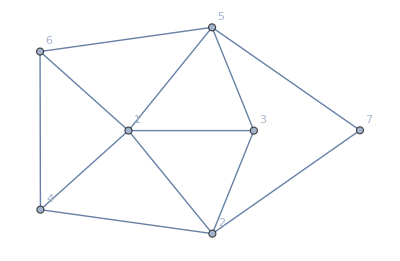
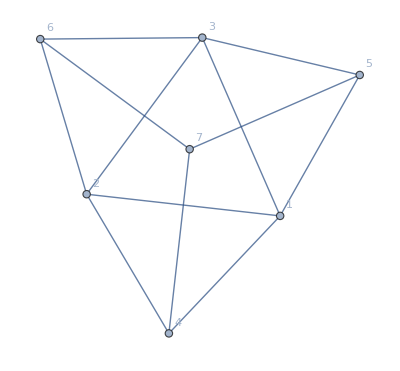

```mathematica
Select[all,CliqueNumber[#]==3&&ChromaticNumber[#]==4&]
```